```mathematica
<<MaTeX`
```

### 2D Zernike moments

```mathematica
(* plotting staff, auxilary functions *)
(* convert expression (fucntion) from polar coordinates to cartesian *)
r2c[e_]:=Simplify[TrigExpand[e]/.{Sin[θ]:>y/r,Cos[θ]:>x/r}/.r^n_:>(x^2+y^2)^(n/2)] 
(*r2c3d[e_]:=Simplify[TrigExpand[e]/.{Sin[θ]:>y/r,Cos[θ]:>z/r, }/.r^n_:>(x^2+y^2+ z^2)^(n/2)] *)
(*  *)
zPlot[e_]:=With[{f= r2c[e]},DensityPlot[  f,{x,-1,1},{y,-1,1},RegionFunction:>(#1^2+#2^2≤1&), PlotPoints->12,Frame->False, ImageSize->120, ColorFunction->"BlueGreenYellow"]]
```

```mathematica
{maxX, maxY} = {11,11};
{dx, dy} = {2/(maxX-1), 2/(maxY-1)};

(* radial polynomials *)
(* n ≥ m , n - m is even *)
R[n_, m_, r_]:=Sum[((-1)^k(n-k)!)/(k! ((n+m)/2 - k)! ((n-m)/2 - k)!)r^(n - 2 k),{k,0, (n - m)/2,1}]

(* Zernike polynomials *)
Z[n_, m_,r_, θ_]:=ZernikeR[Abs@n,Abs@m,r]*If[m ≥0, Cos[m θ], Sin[Abs@m θ]] (*R[n, m, r]*) 
(* Zernike moments for given 2D img *)
A[n_, m_, IMG_] := (m+1)/π Sum[
IMG⟦(maxX - 1)/2 + x/dx+1,(maxY - 1)/2 +  y/dy + 1⟧ r2c[Z[n,m,r,θ]],
{x, -1,1, dx}, {y, -1, 1, dy}]
```

```mathematica
LablAlig={-1.2, 1};
zernikeHarmonics = Grid[
{{Overlay[{zPlot[Z[0,0,r,θ]], MaTeX["Z^{"<>ToString[0]<>"}_{"<> ToString[0]<>"}", Magnification->1.5]}, Alignment->LablAlig]},

Flatten@Table[Overlay[{zPlot[Z[1,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[1]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-1, 1}}],

Table[Overlay[{zPlot[Z[2,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[2]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-2, 0, 2}}],

Table[Overlay[{zPlot[Z[3,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[3]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-3, -1, 1, 3}}],

Table[Overlay[{zPlot[Z[4,m,r,θ]], MaTeX["Z^{"<>ToString[m]<>"}_{"<> ToString[4]<>"}", Magnification->1.5]}, Alignment->LablAlig],{m,{-4, -2, 0, 2, 4}}]
}]
```

-Graphics--Graphics- |  |  |  | 
-Graphics--Graphics- | -Graphics--Graphics- |  |  | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

```mathematica
Export[NotebookDirectory[]<>"/imgs/zernike_mods.pdf",zernikeHarmonics]
```

/home/denys/Documents/ifw/ml/datasciencesnippets/descriptors//imgs/zernike_mods.pdf

#### Test on the 2D points cloud

Test of orthogonality

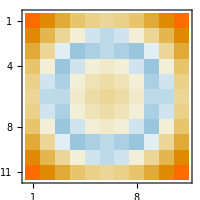

```mathematica
test2DOrt= Table[r2c[Z[4,0,r, θ]]//N(*If[Mod[i+j, 2] == 0, 1,0]*), {x,-1, 1, dx}, {y,-1,1, dy}];

MatrixPlot[test2DOrt, ImageSize->200]
```

```mathematica
Length@test2DOrt
```

11

```mathematica
Table[{nm⟦1⟧, nm⟦2⟧, A[nm⟦1⟧,nm⟦2⟧,test2DOrt]//N},
{nm, {
{0,0}, 
{1,-1},{1,1}, 
{2,-2}, {2,0}, {2,2},
{3,-3},{3,-1},{3,1},{3,3},
{4,-4},{4,-2},{4,0},{4,2},{4,4}
}}]//TableForm
```

0 | 0 | 0.
1 | -1 | 0.
1 | 1 | 41.1654
2 | -2 | -1.06018×10^-16
2 | 0 | 0.
2 | 2 | 0.
3 | -3 | 0.
3 | -1 | 0.
3 | 1 | 114.524
3 | 3 | -92.7823
4 | -4 | 1.27222×10^-15
4 | -2 | -2.65046×10^-17
4 | 0 | 0.
4 | 2 | 0.
4 | 4 | -1.13086×10^-14

```mathematica
(*generators *)
make2DPoint[i_,j_]:=Module[{pointOnPlane},
pointOnPlane = Table[0, {x,-Quotient[maxX,2], Quotient[maxY,2]}, {y,-Quotient[maxX,2], Quotient[maxY,2]}];
pointOnPlane⟦i, j⟧ = -1;
(*pointOnPlane⟦i+2, j+2⟧ = 2;*)
pointOnPlane⟦i, j+2⟧ = -2;
pointOnPlane⟦i, j-2⟧ = -2;
(*pointOnPlane⟦i+2, j⟧ = -2;
pointOnPlane⟦i-2, j⟧ = -2;*)
(*pointOnPlane⟦i, j+1⟧ = 1;*)
(*pointOnPlane⟦i+3, j⟧ = 1;
pointOnPlane⟦i-3, j⟧ = 1;*)
(*pointOnPlane⟦i, j-3⟧ = 1;*)
(*pointOnPlane⟦i, j+3⟧ = 1;*)
pointOnPlane
]

makeDescriptorTable[IMG_]:=Module[{table},
table = Table[{nm⟦1⟧, nm⟦2⟧, A[nm⟦1⟧,nm⟦2⟧,IMG]//N},
{nm, {
{0,0}, 
{1,-1},{1,1}, 
{2,-2}, {2,0}, {2,2},
{3,-3},{3,-1},{3,1},{3,3},
{4,-4},{4,-2},{4,0},{4,2},{4,4}
}}];
table//TableForm
]
```

```mathematica
Manipulate[
Row[{MatrixPlot[make2DPoint[y,x], ImageSize->200], makeDescriptorTable[make2DPoint[x,y]]}],

{{x, (maxX-1)/2 + 1},1, maxX,1, Appearance->"Open"},
{{y, (maxY-1)/2 + 1},1, maxY,1, Appearance->"Open"}
]
```

### 3D Zernike moments

```mathematica
Z3D[n_,l_,m_,r_, θ_, ϕ_]:=ZernikeR[n,l, r]SphericalHarmonicY[l, m, θ, ϕ]
```

```mathematica
DensityPlot3D[
Re[Z3D[1,1,1,r, θ,ϕ]]/.{r->√(x^2+y^2+z^2), θ->ArcTan[√(x^2+y^2), z], ϕ->ArcTan[y , x]},

{x,-1, 1},
{y, -1, 1},
{z,-1, 1},
 PlotPoints->20,
PlotRange->{{-1,1},{-1,1},{-1,1}}
]
```

-Graphics3D-

```mathematica
Re[Z3D[2,1,1,r, θ,ϕ]]/.{r->√(x^2+y^2+z^2), θ->ArcTan[√(x^2+y^2), z], ϕ->ArcTan[y , x]}
```

-1/2 √(3/(2 π)) Re[ⅇ^(ⅈ ArcTan[y,x]) z]